# Quantum Error Correction and Magic State Distillation

By: William Munizzi

### Paclet Installation

```mathematica
PacletInstall[CloudObject["https://wolfr.am/DevWQCF"], ForceVersionInstall -> True]
<< Wolfram`QuantumFramework`
```

PacletObject[…]

## Code Testing

```mathematica
KroneckerProduct[{{1,0},{0,1}},{{0,1},{1,0}}]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
QuantumTensorProduct[QuantumOperator["Identity",{1}],QuantumOperator["PauliX",{2}]]["Matrix"]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
testState={{-Graphics-, QuantumState}}[{1,1},2];
testState["Matrix"]//MatrixForm
```

(1
1)

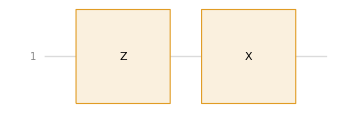

```mathematica
testQC = QuantumCircuitOperator[{QuantumOperator["PauliZ",{1}],QuantumOperator["PauliX",{1}]}];
testQC["Diagram"]
```

```mathematica
testQC[testState]["Matrix"]//MatrixForm
```

(-1
1)

```mathematica
Exp[ⅈ #]&/@{0,π/2,π,3π/2}
```

{1,ⅈ,-1,-ⅈ}

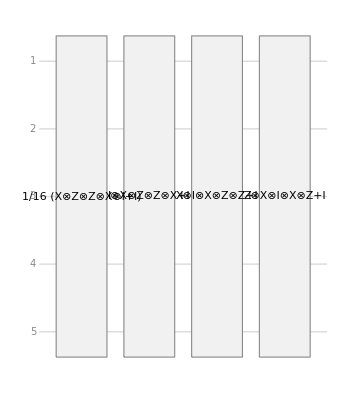

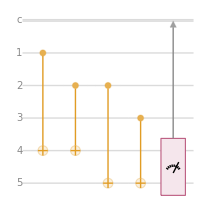

```mathematica
encodingQC=QuantumCircuitOperator[{QuantumOperator["CNOT",{1,4}],QuantumOperator["CNOT",{2,4}],QuantumOperator["CNOT",{2,5}],QuantumOperator["CNOT",{3,5}],QuantumMeasurementOperator[{4,5}]}];
encodingQC["Diagram"]
```

```mathematica
(*Why is it projecting onto 2 qubits upon measurement? Options should only be 0 and 1.*)
FaultyTState[.3]["Amplitudes"]
```

<|00→0.61547,01→0.11547-0.11547 ⅈ,10→0.11547+0.11547 ⅈ,11→0.38453|>

```mathematica
testρ = QuantumState["RandomMixed"];
testσ = QuantumState["RandomMixed"];
```

```mathematica
FullTFidelityFunction[ρ_,σ_]:=Block[{trP = Tr[N[ρ]],trS=Tr[N[σ]],trace},
trace = Tr[MatrixPower[MatrixPower[ρ/trP,.5].(σ/trS).MatrixPower[ρ/trP,.5],.5]];
trace^2];

FullTFidelityFunction[testρ["DensityMatrix"],testσ["DensityMatrix"]]

QuantumDistance[testρ["Normalized"],testσ["Normalized"],"Fidelity"]
```

0.336666+2.36962×10^-18 ⅈ

```mathematica
QuantumDistance[testρ["Normalized"],testσ["Normalized"],"Fidelity"]
```

0.336666

```mathematica
FullTFidelity[ρ_,LocalAction_]:=Block[{CliffordSet = LocalAction},Max[Abs/@Table[QuantumDistance[ρ["Normalized"],QuantumOperator[][stateT0]["Normalized"],"Fidelity"],{j,Length[CliffordSet]}]]];
```

## Error-Correcting Codes

Here we present a collection of error-correcting protocols and associated applications for quantum computing.

## 5-Qubit Code

### Definition

We begin with the 5-qubit error-correcting code, the smallest code that can protect against arbitrary single-qubit error. In this scheme, one logical qubit is encoded into five physical qubits. We define the following set of four stabilizer operations that generating the 5-qubit code.

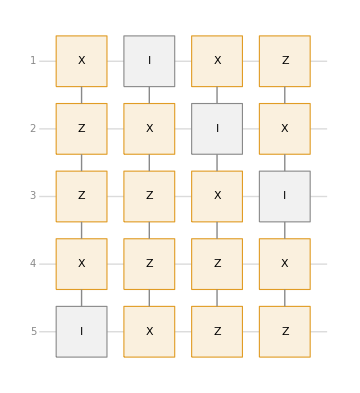

```mathematica
s1 = QuantumOperator["XZZXI"];
s2 = QuantumOperator["IXZZX"];
s3 = QuantumOperator["XIXZZ"];
s4 = QuantumOperator["ZXIXZ"];

stabilizers={s1,s2,s3,s4};

QuantumCircuitOperator[stabilizers]["Diagram"]
```

Here we define a circuit to project a 5-qubit system into the code subspace for this error-correcting scheme. This code subspace is the two-dimensional Hilbert space containing states upon which the above stabilizing operations act trivially (). We therefore can define the projecting operation as below.

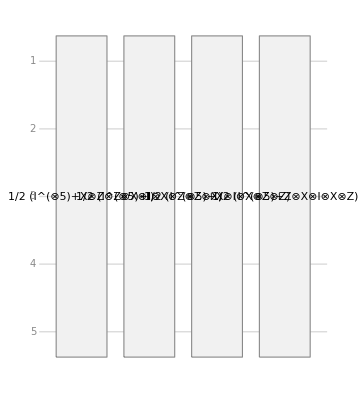

```mathematica
subspaceProjectorFiveQCode=QuantumCircuitOperator[{1/2(("I"->Range[5])+"XZZXI"),1/2(("I"->Range[5])+"IXZZX"),1/2(("I"->Range[5])+"XIXZZ"),1/2(("I"->Range[5])+"ZXIXZ")}];
subspaceProjectorFiveQCode["Diagram"]
```

Note: Operations on the logical stored information, such as Pauli-X and Pauli-Z operations,  are defined as below.

```mathematica
logicalX = QuantumOperator["X"->Range[5]];
logicalZ = QuantumOperator["Z"->Range[5]];
```

## 7-Qubit Code (Steane Code)

### Definition

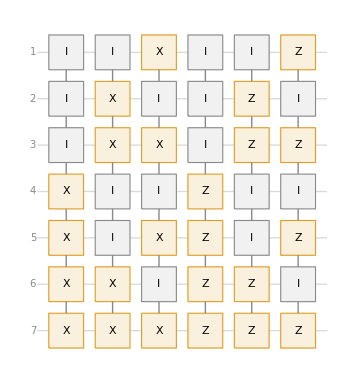

```mathematica
SteaneCodeS1 = QuantumOperator["IIIXXXX"];
SteaneCodeS2 = QuantumOperator["IXXIIXX"];
SteaneCodeS3 = QuantumOperator["XIXIXIX"];
SteaneCodeS4 = QuantumOperator["IIIZZZZ"];
SteaneCodeS5 = QuantumOperator["IZZIIZZ"];
SteaneCodeS6 = QuantumOperator["ZIZIZIZ"];

SteaneStabilizers={SteaneCodeS1,SteaneCodeS2,SteaneCodeS3,SteaneCodeS4,SteaneCodeS5,SteaneCodeS6};

QuantumCircuitOperator[SteaneStabilizers]["Diagram"]
```

```mathematica
SteaneLogicalX = QuantumOperator["XXXXXXX"];
SteaneLogicalZ = QuantumOperator["ZZZZZZZ"];
```

```mathematica
SteaneLogical0 =  Total[QuantumState/@{"0000000","0001111","0110011","0111100","1010101","1011010","1100110","1101001"}];

SteaneLogical1 = SteaneLogicalX[SteaneLogical0];

ψ7[C1_,C2_]:= C1*SteaneLogical0+C2*SteaneLogical1;
```

```mathematica
test7State = ψ7[1/Sqrt[2],1/Sqrt[2]];
QuantumCircuitOperator[SteaneStabilizers][test7State]
```

QuantumState[…]

### Fault-Tolerance

## 9-Qubit Code (Shor Code)

### Definition

The famous 9-qubit Shor Code encodes a single logical qubit into nine physical qubits to correct arbitrary single-qubit error. We simulate the arbitrary corruption of a single qubit by applying a unitary transform, defined as some linear combination of Pauli operations, that acts on a random qubit of the system.

```mathematica
SingleBitUnitaryError[{c1_,c2_,c3_,c4_}]:=c1* QuantumOperator["I"]+c2* QuantumOperator["X"]+c3* QuantumOperator["Y"]+c4* QuantumOperator["Z"];

NoisyChannel = QuantumOperator[SingleBitUnitaryError[RandomSample[.01*RandomChoice[IntegerPartitions[100,{4}]]]]];

NC = QuantumCircuitOperator[NoisyChannel,{RandomInteger[{1,9}]}];
```

```mathematica
NoisyChannel["Matrix"]//MatrixForm
```

(0.93+0. ⅈ | 0.03-0.04 ⅈ
0.03+0.04 ⅈ | 0.07+0. ⅈ)

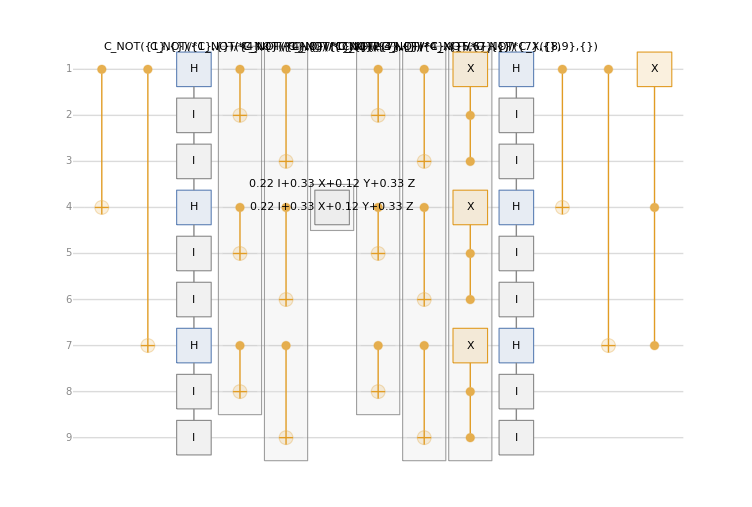

```mathematica
ShorCodeS1 = QuantumOperator["CNOT",{1,4}];
ShorCodeS2 = QuantumOperator["CNOT",{1,7}];
ShorCodeS3 = QuantumOperator["HIIHIIHII"];
ShorCodeS4 = QuantumCircuitOperator[{QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{4,5}],QuantumOperator["CNOT",{7,8}]}];
ShorCodeS5 = QuantumCircuitOperator[{QuantumOperator["CNOT",{1,3}],QuantumOperator["CNOT",{4,6}],QuantumOperator["CNOT",{7,9}]}];
ShorCodeS6 =QuantumCircuitOperator[{QuantumOperator[{"C","X"->{1},{2,3}}],QuantumOperator[{"C","X"->{4},{5,6}}],QuantumOperator[{"C","X"->{7},{8,9}}]}] ;
ShorCodeS7 = QuantumOperator[{"C","X"->{1},{4,7}}];

ShorStabilizers={ShorCodeS1,ShorCodeS2,ShorCodeS3,ShorCodeS4,ShorCodeS5,NC,ShorCodeS4,ShorCodeS5,ShorCodeS6,ShorCodeS3,ShorCodeS1,ShorCodeS2,ShorCodeS7};

QuantumCircuitOperator[ShorStabilizers]["Diagram"]
```

```mathematica
ShorLogical0 =  (1/Sqrt[8])*QuantumTensorProduct[QuantumState["000"]+QuantumState["111"],QuantumState["000"]+QuantumState["111"],QuantumState["000"]+QuantumState["111"]];

ShorLogical1 = (1/Sqrt[8])*QuantumTensorProduct[QuantumState["000"]-QuantumState["111"],QuantumState["000"]-QuantumState["111"],QuantumState["000"]-QuantumState["111"]];

ψShor[C1_,C2_]:= C1*ShorLogical0+C2*ShorLogical1;
```

```mathematica
testShorState = ψShor[1/Sqrt[2],1/Sqrt[2]];
QuantumCircuitOperator[ShorStabilizers][testShorState]
```

QuantumState[…]

### Fault-Tolerance

## Bosonic Codes

## Toric Code

## Magic State Distillation

## Magic State Distillation

Magic states are a valuable resource for realizable universal quantum computation. It is famously known that the set of Clifford gates (Hadamard, phase, CNOT gates) are not themselves a universal set, however access to Clifford gates and one additional non-Clifford operation does provide a universal gate set. For this reason, much interest surrounds the acquisition of non-Clifford resources by simplest means available. In 2004 Sergey Bravyi and Alexei Kitaev demonstrated that stabilizer circuits, those circuits composed only of Clifford gates, could be used to imperfectly (probabilistically) access non-stabilizer states (those states not directly reachable from measurement basis using only Clifford operations). As a protocol, so-called “Magic States” of a given qubit-number are distilled from higher-qubit systems constructed in a noise-assumptive manner.  Using an error-correcting scheme, higher-fidelity magic states can be extracted from the larger, faulty composite system. Once one has produced a magic state of sufficiently-high fidelity for computational viability, the state may be implemented as a non-Clifford resource in the appropriate quantum circuit, thus offering universal computation capabilities.

### Distilling T-Type Magic

Define T-operator and associated eigenstates.

```mathematica
operatorT = QuantumOperator[Exp[I*Pi/4]/Sqrt[2]*{{1,1},{I,-I}},{1},"Z"];

β = 1/2*ArcCos[1/Sqrt[3]];

stateT0 = Cos[β]*QuantumState[{1,0},2] + Exp[I*Pi/4]*Sin[β]*QuantumState[{0,1},2];
stateT1 = Sin[β]*QuantumState[{1,0},2] - Exp[I*Pi/4]*Cos[β]*QuantumState[{0,1},2];
```

Applying projection operation on the 5-fold tensor product of T0, encodes a logical T0 state into 5 physical qubits. Accordingly, with T1. This corresponds to an orthogonal projection into the code subspace.

```mathematica
logicalT0 = subspaceProjectorFiveQCode[QuantumTensorProduct[stateT0,stateT0,stateT0,stateT0,stateT0]];
logicalT1 = subspaceProjectorFiveQCode[QuantumTensorProduct[stateT1,stateT1,stateT1,stateT1,stateT1]];
```

Define a function for producing a faulty version of a T-state based on some initial dephasing operation. An arbitrary input error is assumed and applied at the state-preparation stage, for example, with ϵ = 0.3 below.

```mathematica
FaultyTState[inputError_]:=QuantumState[(1-inputError)*stateT0["DensityMatrix"]+ inputError*stateT1["DensityMatrix"]]; 
FaultyTState[.3]["DensityMatrix"]//MatrixForm
```

(0.61547 | 0.11547-0.11547 ⅈ
0.11547+0.11547 ⅈ | 0.38453)

Define a decoding circuit for purifying a single-qubit T-state from 5-qubit product state. This procedure extracts a single output state from the multi-qubit input. The fidelity of the final output state can then be analyzed.

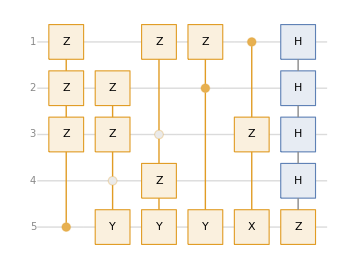

```mathematica
decodingQC = QuantumCircuitOperator[{QuantumOperator[{"C","Z"->{1,2,3},{5}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{2,3}},{4}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{1,4}},{3}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{1}},{2}}],QuantumOperator[{"C",{"X"->{5},"Z"->{3}},{1}}],QuantumOperator[{"H"->{1,2,3,4},"Z"->{5}}]}];
decodingQC["Diagram"]
```

### Results and Fault-Tolerance Threshold

Here we establish the fault-tolerant threshold for this distillation protocol, the characteristic error-threshold below which quantum error-correction is effective and logical errors can be suppressed. Successful distillation of magic T-states corresponds to detection of the trivial syndrome upon measurement, i.e. no logical operation was performed on the stored information. The probability of detecting this trivial syndrome can be computed by projecting a faulty T-state, with some initial input error, into the code subspace and subsequently tracing out over the four ancillary qubits. The plot below considers this calculation for a range of input errors.

```mathematica
ϵinput = Range[0.,.5,.5/100];
```

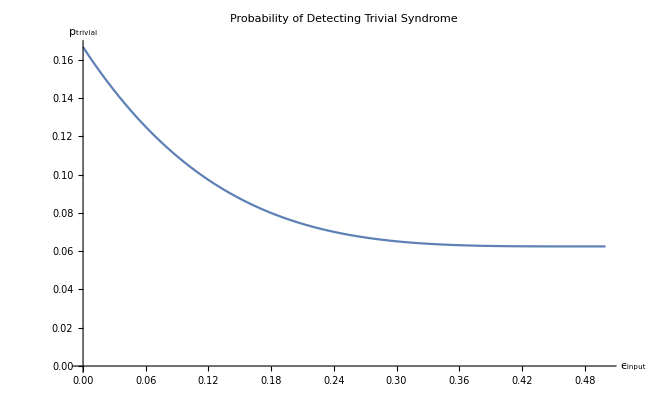

```mathematica
syndromeProb = Table[Tr[QuantumPartialTrace[subspaceProjectorFiveQCode[QuantumTensorProduct[FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]]]],{1,2,3,4}]],{i,Length[ϵinput]}];

ListLinePlot[Thread[{ϵinput,syndromeProb}],{PlotRange-> All,PlotLabel-> Style["Probability of Detecting Trivial Syndrome", Large],AxesLabel-> {Style["ϵ_input",Medium],Style["p_trivial",Medium]}}]
```

Similarly the error in the distilled state can be computed as a function of input error, thereby observing the production of a higher-fidelity T-state from the tensor product of multiple lower-fidelity copies. A fidelity calculation allows for a comparison of the output error with the input error. Note: The decoding operation actually produces the state T1, which can be transformed back into T0 by a Hadamard gate followed by a Pauli-Y gate.

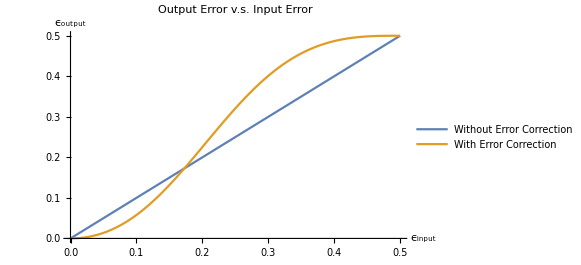

```mathematica
ϵoutput = Flatten[Table[1-First@stateT0["Conjugate"]["Transpose"]["Matrix"].QuantumOperator[{"Y"}][QuantumOperator[{"H"}][QuantumPartialTrace[decodingQC[subspaceProjectorFiveQCode[QuantumTensorProduct[FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]],FaultyTState[ϵinput[[i]]]]]]["Normalized"],{1,2,3,4}]]]["DensityMatrix"].stateT0["Matrix"],{i,Length[ϵinput]}]];

ListLinePlot[{Thread[{ϵinput,ϵinput}],Thread[{ϵinput,ϵoutput}]},{PlotRange-> All,PlotLabel-> Style["Output Error v.s. Input Error", Large],AxesLabel-> {Style["ϵ_input",Medium],Style["ϵ_output",Medium]},PlotLegends-> {"Without Error Correction","With Error Correction"}}]
```

### Distilling H-Type Magic

Define A-operator and associated eigenstates.

```mathematica
operatorA = (1/Sqrt[2])*(QuantumOperator["X"]+QuantumOperator["Y"]);
operatorA["Matrix"]//MatrixForm

stateA0 = (1/Sqrt[2])*(QuantumState[{1,0},2] + Exp[I*Pi/4]*QuantumState[{0,1},2]);
stateA1 = QuantumOperator["Z"][stateA0];
```

(0 | (1-ⅈ)/(√2)
(1+ⅈ)/(√2) | 0)

The maximum fidelity of an arbitrary state with A_0 can be computed as,

```mathematica
MaxAFidelity[ρ_]:=Sqrt[First[Flatten[stateA0["Conjugate"]["Transpose"]["Matrix"].ρ["DensityMatrix"].stateA0["Matrix"]]]];

MaxAFidelity[QuantumState["RandomMixed"]]
```

1.34867+0. ⅈ

A faulty H-state can be prepared similarly to the faulty T-state production above,

```mathematica
FaultyHState[inputError_]:=QuantumState[(1-inputError)*stateA0["DensityMatrix"]+ inputError*stateA1["DensityMatrix"]];
```

Applying projection operation on the 15-fold tensor product of A0,

```mathematica
(*Below in progress.*)
```

```mathematica
subspaceProjectorA = QuantumCircuitOperator[{QuantumOperator[{"C","Z"->{1,2,3},{5}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{2,3}},{4}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{1,4}},{3}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{1}},{2}}],QuantumOperator[{"C",{"X"->{5},"Z"->{3}},{1}}],QuantumOperator[{"H"->{1,2,3,4},"Z"->{5}}]}]

subspaceProjectorZ = QuantumCircuitOperator[{QuantumOperator[{"C","Z"->{1,2,3},{5}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{2,3}},{4}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{1,4}},{3}}],QuantumOperator[{"C",{"Y"->{5},"Z"->{1}},{2}}],QuantumOperator[{"C",{"X"->{5},"Z"->{3}},{1}}],QuantumOperator[{"H"->{1,2,3,4},"Z"->{5}}]}]

HStateSubspaceProjector = QuantumCircuitOperator[{subspaceProjectorA,subspaceProjectorZ}];
```

QuantumCircuitOperator[…]

```mathematica
logicalA0 = HStateSubspaceProjector[QuantumTensorProduct[stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0,stateA0]];
logicalA1 = HStateSubspaceProjector[QuantumTensorProduct[stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1,stateA1]];
```

QuantumCircuitOperator::dim: Circuit expecting dimensions {2,2,2,2,2}, but the state has dimensions {2,2,2,2,2,2,2,2,2,2,«5»}.

### Fault-Tolerance Threshold

## Non-Local Magic Distillation

It was shown in [arXiv: 2106.12591] that one can distill non-locally store magic from many-body entangled states. Using the Bravyi-Kitaev distillation protocol outlined above, one can demonstrate successful T-type magic distillation from non-product input states. Two example states are the standard GHZ state with relative phase, defined , and a GHZ-like state in the T-basis defined,  .

Begin first by defining functions to construct the Phase-GHZ and GHZ-T states of desired dimension, weighting, and relative phase.

```mathematica
statePG[α_,ϕ_,n_]:= α*QuantumTensorProduct@ConstantArray[QuantumState["0"],n]+Exp[I*ϕ]*Sqrt[1-α^2]*QuantumTensorProduct@ConstantArray[QuantumState["1"],n];

stateGT[α_,ϕ_,n_]:= α*QuantumTensorProduct@ConstantArray[stateT0,n]+Exp[I*ϕ]*Sqrt[1-α^2]*QuantumTensorProduct@ConstantArray[stateT1,n];
```

Define a function that computes T-fidelity of a given state, i.e. a measurement of fidelity between a chosen state and any state reachable from T0 through only local transformations. The user inputs a test state and set of unitary operations. For completeness, a full set of local transformations should be provided.

```mathematica
FullTFidelity[ρ_,UnitaryCircuit_]:=Max[Abs/@Table[QuantumDistance[ρ["Normalized"],UnitaryCircuit[[j]][stateT0]["Normalized"],"Fidelity"],{j,Length[UnitaryCircuit]}]];
```

We can now analyze the viability of distilling high-fidelity T-type magic from these states as a function of parameter α. These values will be compared to the distilled fidelity from 5 copies of a faulty-T product state as explored in the last section. All distilled states distilled with fidelity above the BK threshold are considered successful and viable for fault-tolerant application. Note that .

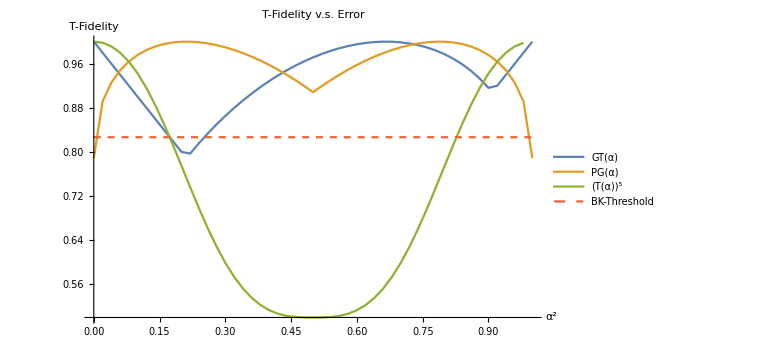

```mathematica
αSquared = Range[0.,1.,1./50];

plotGT = Table[FullTFidelity[QuantumPartialTrace[decodingQC[subspaceProjectorFiveQCode[stateGT[Sqrt[αSquared[[i]]],0.,5]]]["Normalized"],{1,2,3,4}],phaseRemovedCircuits],{i,Length[αSquared]}];

plotPG = Table[FullTFidelity[QuantumPartialTrace[decodingQC[subspaceProjectorFiveQCode[statePG[Sqrt[αSquared[[i]]],Pi/4,5]]]["Normalized"],{1,2,3,4}],phaseRemovedCircuits],{i,Length[αSquared]}];

plotProduct = Table[QuantumDistance[QuantumPartialTrace[decodingQC[subspaceProjectorFiveQCode[QuantumTensorProduct[FaultyTState[αSquared[[i]]],FaultyTState[αSquared[[i]]],FaultyTState[αSquared[[i]]],FaultyTState[αSquared[[i]]],FaultyTState[αSquared[[i]]]]]]["Normalized"],{1,2,3,4}],stateT0,"Fidelity"],{i,Length[αSquared]}];


thresholdLine = ConstantArray[0.8267137522242428,Length[αSquared]];

ListLinePlot[{Thread[{αSquared,plotGT}],Thread[{αSquared,plotPG}],Join[Reverse[Thread[{1-αSquared,plotProduct}]][[1;;25]],Thread[{αSquared,plotProduct}][[26;;50]]],Style[Thread[{αSquared,thresholdLine}],Dashed]},PlotRange->{0.5,1.0},PlotLabel->Style["T-Fidelity v.s. Error",Large],AxesLabel->{Style["α^2",Medium],Style["T-Fidelity",Medium]},PlotLegends->{Ket["GT(α)"],Ket["PG(α)"],Ket["T(α)"]^5,"BK-Threshold"}]
```

Important to note, stabilizer measurement is only defined up to global phase of , therefore we mod out by this overall phase when considering quantum circuits that produce the same measurable output state.

```mathematica
ω = Exp[2*Pi*I/8];
GlobalPhaseCongruence[x_,y_]:=If[Or[x==ω*y,x==(ω)^2*y,x==(ω)^3*y,x==(ω)^4*y,x==(ω)^5*y,x==(ω)^6*y,x==(ω)^7*y,x==(ω)^8*y],True, False];

GlobalPhaseCongruence[QuantumOperator["H"],I*QuantumOperator["H"]]
GlobalPhaseCongruence[QuantumOperator["H"],-2*QuantumOperator["H"]]

GlobalPhaseCongruence[QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["S"]}]["Matrix"],I*QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["S"]}]["Matrix"]]
```

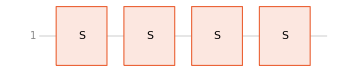

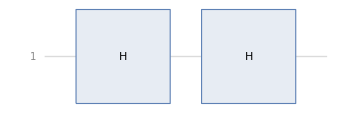

```mathematica
QuantumCircuitOperator[{QuantumOperator["S"],QuantumOperator["S"],QuantumOperator["S"],QuantumOperator["S"]}]["Diagram"]
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["H"]}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{QuantumOperator["S"],QuantumOperator["S"],QuantumOperator["S"],QuantumOperator["S"]}]==QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["H"]}]
```

True

```mathematica
gates = Flatten[Join[Table[Tuples[{QuantumOperator["S"],QuantumOperator["H"]},k],{k,5}]],1];
Length[gates]
circuits = Table[QuantumCircuitOperator[gates[[l]]],{l,Length[gates]}];
phaseRemovedCircuits = First/@Gather[circuits,GlobalPhaseCongruence[#1["Matrix"],#2["Matrix"]]&];
Length[phaseRemovedCircuits]
(*Why does this not delete equivalent circuits when it clearly recognizes them as equal?*)
```

62

Gather::smtst: Application of the SameTest function yielded …, which evaluates to …. The SameTest function must evaluate to True or False at every pair of elements.

General::stop: Further output of Gather::smtst will be suppressed during this calculation.

28

```mathematica
phaseRemovedCircuits
```

{QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…]}

```mathematica
Gather[circuits[[;;15]],GlobalPhaseCongruence[#1["Matrix"],#2["Matrix"]]&]
```

{{QuantumCircuitOperator[…],QuantumCircuitOperator[…],QuantumCircuitOperator[…]},{QuantumCircuitOperator[…],QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…],QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]},{QuantumCircuitOperator[…]}}